```mathematica
generateTrials[nDays_, nTrials_, nPeople_]:= Module[{},
SeedRandom[1234];
RandomChoice[Range[nDays], {nTrials, nPeople}]
];

generateSingleTrial[nDays_, nPeople_]:= Module[{},
(* No seeding -- each trial results in different values *)
RandomChoice[Range[nDays], {1, nPeople}]
];

generateWeightedTrials[nDays_, nTrials_, nPeople_]:= Module[{weights},
SeedRandom[3456];
weights = RandomInteger[{1,3}, nDays];
RandomChoice[weights->Range[nDays], {nTrials, nPeople}]
];

generateSingleWeightedTrial[nDays_, nPeople_]:= Module[{weights},
weights = RandomInteger[{1,3}, nDays];
RandomChoice[weights->Range[nDays], {1, nPeople}]
];

gatherIntoGroups[trialSet_, daysApart_]:= Module[{},
If[MatrixQ[trialSet],
	Table[Gather[trialSet[[i]], Abs[#1 - #2] < daysApart+1 &],{i,1,Length[trialSet]}], 
	Gather[trialSet, Abs[#1 - #2] < daysApart+1 &]]
];

occurs[group_, nSharing_]:= Length[Select[group, Length[#]≥  nSharing &]];

probSharing[groups_, nSharing_]:= Module[{a, prob},
	a = occurs[#, nSharing] & /@ groups;
  prob = Divide[Length[Select[a, # ≥ 1 &]], Length[groups]] // N
];
```

```mathematica
birthdayModel[nDays_, nTrials_, nPeople_, daysApart_, nSharing_]:= Module[{dataSet, groups, prob}, 
dataSet = generateTrials[nDays, nTrials, nPeople];
groups = gatherIntoGroups[dataSet, daysApart];
prob = probSharing[groups, nSharing]
];
```

```mathematica
(* Instead of creating all the trials first, just create one trial at a time and count up the evolution of probability as the number of trials increases. This is faster. *)
```

```mathematica
birthdayTrialOutcome[nDays_, nPeople_, daysApart_, nSharing_]:= Module[{trial, groups, instances, result},
(* Fix the number of trials to be 1 *)
trial = generateSingleTrial[nDays,nPeople];
groups = First[gatherIntoGroups[trial, daysApart]];
instances = Length[Select[groups, Length[#] ≥  nSharing &]];
result = If[instances ≥ 1, 1, 0]
];
```

```mathematica
birthdayWeightedTrialOutcome[nDays_, nPeople_, daysApart_, nSharing_]:= Module[{trial, groups, instances, result},
(* Fix the number of trials to be 1 *)
trial = generateSingleWeightedTrial[nDays,nPeople];
groups = First[gatherIntoGroups[trial, daysApart]];
instances = Length[Select[groups, Length[#] ≥  nSharing &]];
result = If[instances ≥ 1, 1, 0]
];
```

```mathematica
birthdayModelFast[nDays_, nTrials_, nPeople_, daysApart_, nSharing_]:= Module[{outcomes, prob},
outcomes =  Table[birthdayTrialOutcome[nDays, nPeople, daysApart, nSharing], {i, 1, nTrials}];
prob = Divide[Length[Select[outcomes, # == 1 &]], Length[outcomes]] //N
];
```

```mathematica
birthdayModelWeightedFast[nDays_, nTrials_, nPeople_, daysApart_, nSharing_]:= Module[{outcomes, prob},
outcomes =  Table[birthdayWeightedTrialOutcome[nDays, nPeople, daysApart, nSharing], {i, 1, nTrials}];
prob = Divide[Length[Select[outcomes, # == 1 &]], Length[outcomes]] //N
];
```

```mathematica
nDays = {100, 200, 300, 400, 500, 600, 700};
```

```mathematica
daysF = birthdayModelFast[#, 500, 50, 0, 2] & /@ {100, 200, 300, 400, 500, 600, 700}
```

{1.,1.,0.982,0.946,0.914,0.878,0.808}

```mathematica
days = {nDays, daysF}ᵀ
```

{{100,1.},{200,1.},{300,0.982},{400,0.946},{500,0.914},{600,0.878},{700,0.808}}

```mathematica
daysW = birthdayModelWeightedFast[#, 500, 50, 0, 2] & /@ {100, 200, 300, 400, 500, 600, 700}
```

{1.,0.998,0.994,0.982,0.96,0.916,0.864}

```mathematica
daysWF = {nDays, daysW}ᵀ
```

{{100,1.},{200,0.998},{300,0.994},{400,0.982},{500,0.96},{600,0.916},{700,0.864}}

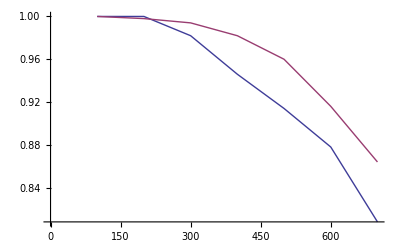

```mathematica
ListLinePlot[{days, daysWF}]
```

```mathematica
g2[nDays_, daysApart_, nSharing_]:= birthdayModelFast[nDays, 500, #, daysApart, nSharing] & /@ Table[i, {i, 20, 60, 5}];
```

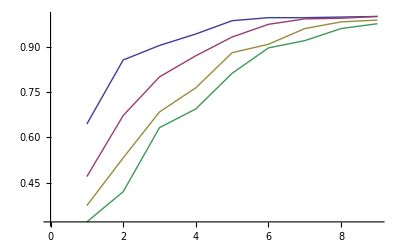

```mathematica
ListLinePlot[g2[#, 0, 2] & /@ {200, 300, 400, 500}]
```

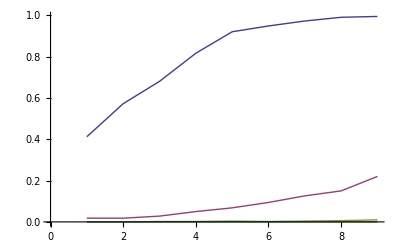

```mathematica
ListLinePlot[g2[365, 0, #]& /@ {2,3,4,5}]
```

```mathematica
Manipulate[ListLinePlot[g2[365, 0, matches]], {matches, {2,3,4,5}}]
```

ListLinePlot::lpn: g2[365.,0.,2.] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[birthdayModel[calendarDays, 1000, people, daysApart, sharing], {people, {10, 20, 30, 40, 50, 60, 70, 80}}, {calendarDays, {300, 365, 366, 400}},{sharing, {2, 3, 4, 5}}, {daysApart, {0,1,2,3,4,5,10}}]
```

```mathematica
g[calendarDays_,daysApart_, nSharing_]:= birthdayModel[calendarDays, 1000, #, daysApart, nSharing] & /@ Range[100];
```

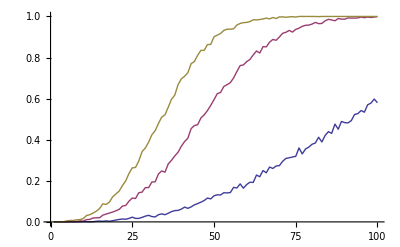

```mathematica
ListLinePlot[g[400,#, 3] & /@ {0,1, 2}]
```

```mathematica
(* Generate the results for plotting and comparing *)
```

```mathematica
(* 300 calendar days; number of people sharing birthdays goes from 2 to 4; birthdays are considered shared if they are within 0 to 3 days apart *)
```

```mathematica
a3002 = g[300, #, 2] & /@ {0,1,2,3};
```

```mathematica
a3003 = g[300, #, 3] & /@ {0,1,2,3};
```

```mathematica
a3004 = g[300, #, 4] & /@ {0,1,2,3};
```

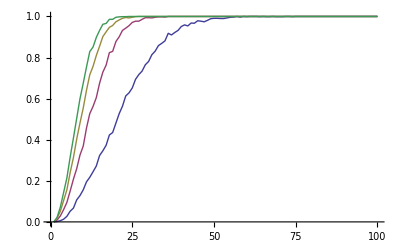
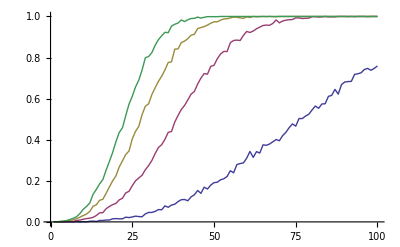
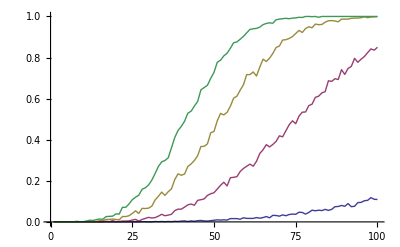

```mathematica
ListLinePlot[#] & /@ {a3002, a3003,a3004}
```

```mathematica
(* 365 calendar days; number of people sharing birthdays goes from 2 to 4; birthdays are considered shared if they are within 0 to 3 days apart *)
```

```mathematica
a3652 = g[365, #, 2] & /@ {0,1,2,3};
```

```mathematica
a3653 = g[365, #, 3] & /@ {0,1,2,3};
```

```mathematica
a3654 = g[365, #, 4] & /@ {0,1,2,3};
```

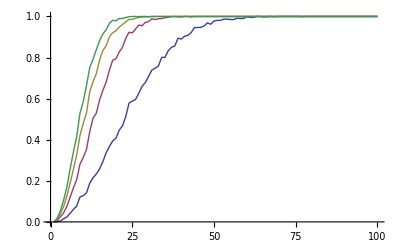
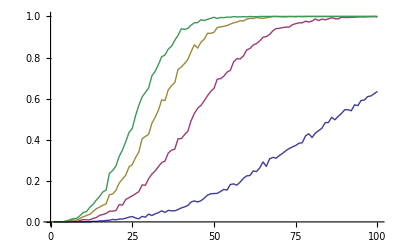
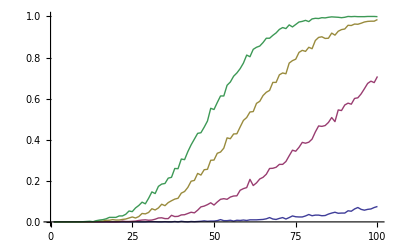

```mathematica
ListLinePlot[#] & /@ {a3652, a3653,a3654}
```

```mathematica
(* 366 calendar days; number of people sharing birthdays goes from 2 to 4; birthdays are considered shared if they are within 0 to 3 days apart *)
```

```mathematica
a3662 = g[366, #, 2] & /@ {0,1,2,3};
```

```mathematica
a3663 = g[366, #, 3] & /@ {0,1,2,3};
```

```mathematica
a3664 = g[366, #, 4] & /@ {0,1,2,3};
```

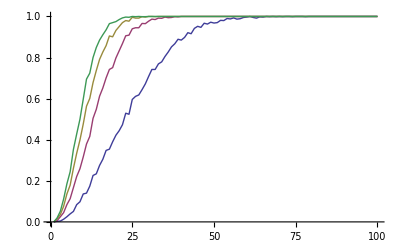
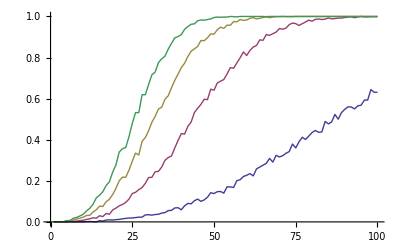
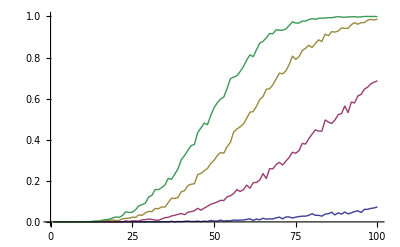

```mathematica
ListLinePlot[#] & /@ {a3662, a3663,a3664}
```

```mathematica
(* 400 calendar days; number of people sharing birthdays goes from 2 to 4; birthdays are considered shared if they are within 0 to 3 days apart *)
```

```mathematica
a4002 = g[400, #, 2] & /@ {0,1,2,3};
```

```mathematica
a4003 = g[400, #, 3] & /@ {0,1,2,3};
```

```mathematica
a4004 = g[400, #, 4] & /@ {0,1,2,3};
```

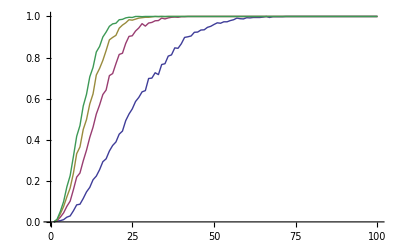
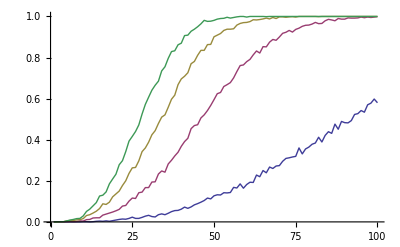
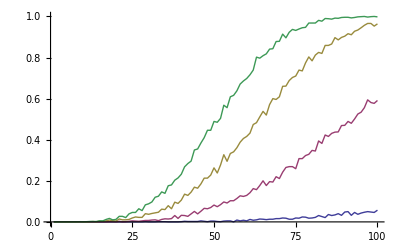

```mathematica
ListLinePlot[#] & /@ {a4002, a4003,a4004}
```

```mathematica
(* Birthdates are not equally probable -- people are more likely to be born on some dates than others *)
(* This is handled by using non-equal weights for the calendar days in generating the data set *)
```

```mathematica
weights = RandomInteger[{1,5}, 365]
```

{1,3,1,1,5,2,2,4,4,2,2,5,5,4,2,4,5,5,2,2,5,2,2,1,5,4,2,4,2,3,4,3,4,3,1,1,3,1,2,1,5,4,1,4,5,5,5,1,3,3,3,5,5,3,1,1,5,2,2,1,1,2,2,2,2,1,3,2,1,5,2,3,4,3,4,1,3,2,4,3,3,3,5,1,3,3,4,4,2,1,4,4,5,3,5,5,1,2,2,4,4,1,3,5,3,2,3,3,3,2,3,2,1,5,3,2,1,4,3,4,2,4,5,5,3,4,3,1,3,3,4,4,2,5,2,4,4,5,4,3,3,5,1,3,4,5,1,5,5,2,1,5,5,4,5,5,4,4,1,2,5,1,3,2,3,3,2,4,2,4,1,3,3,5,3,4,4,3,3,1,2,2,2,3,4,2,5,4,4,3,4,1,4,3,3,4,3,5,3,1,3,5,2,5,5,1,1,5,5,4,2,1,2,5,2,2,5,4,3,3,2,1,5,3,2,1,5,1,2,3,2,4,4,2,2,1,2,5,5,2,4,3,3,4,2,3,1,1,3,1,4,5,4,4,3,2,1,2,1,4,4,2,4,1,1,3,3,1,2,4,3,4,4,3,2,2,2,5,1,5,2,3,4,2,2,2,1,5,3,3,4,3,5,4,1,4,3,5,5,1,4,1,4,1,3,1,2,5,4,1,1,4,4,3,5,2,3,4,3,5,4,5,4,3,1,5,5,4,3,4,2,3,2,4,1,2,4,1,4,2,5,1,5,3,4,2,1,3,4,1,4,2,1,2,2,4,3,1,1,4,3,4,2,2,3}

```mathematica
generateWeightedTrials[365, 3, 10]
```

{{95,54,233,43,64,31,140,141,2,277},{121,164,27,296,247,172,357,197,254,129},{218,253,119,200,121,84,83,279,60,182}}

```mathematica
birthdayModelWeighted[nDays_, nTrials_, nPeople_, daysApart_, nSharing_]:= Module[{dataSet, groups, prob}, 
dataSet = generateWeightedTrials[nDays, nTrials, nPeople];
groups = gatherIntoGroups[dataSet, daysApart];
prob = probSharing[groups, nSharing]
];
```

```mathematica
h[calendarDays_,daysApart_, nSharing_]:= birthdayModelWeighted[calendarDays, 1000, #, daysApart, nSharing] & /@ Range[100];
```

```mathematica
h[365,0,2]
```

{0.,0.002,0.01,0.017,0.031,0.048,0.061,0.08,0.109,0.133,0.167,0.196,0.223,0.255,0.27,0.308,0.341,0.386,0.413,0.447,0.473,0.531,0.556,0.581,0.607,0.645,0.673,0.699,0.71,0.723,0.781,0.796,0.818,0.829,0.845,0.862,0.878,0.897,0.899,0.907,0.932,0.938,0.937,0.951,0.957,0.964,0.978,0.972,0.98,0.982,0.99,0.984,0.99,0.987,0.992,0.989,0.993,0.996,0.997,0.995,0.998,0.999,0.999,0.999,1.,1.,1.,1.,1.,0.999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

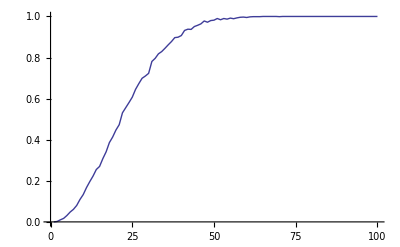

```mathematica
ListLinePlot[%]
```

```mathematica
(* 365 calendar days but unequally weighted -- some days are three times more likely to have births than others; number of people sharing birthdays goes from 2 to 4; birthdays are considered shared if they are within 0 to 3 days apart *)
```

```mathematica
w3652 = h[365, #, 2] & /@ {0,1,2,3};
```

```mathematica
w3653 = h[365, #, 3] & /@ {0,1,2,3};
```

```mathematica
w3654 = h[365, #, 4] & /@ {0,1,2,3};
```

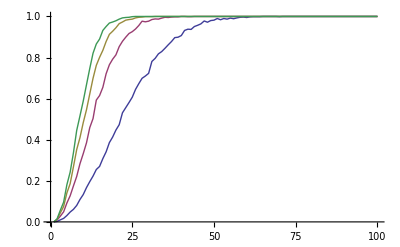
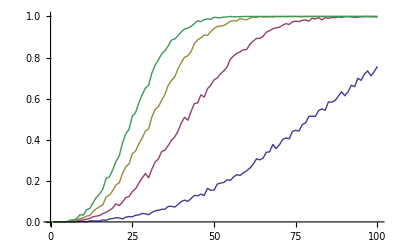
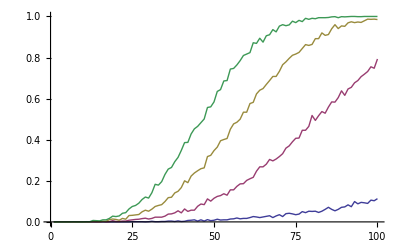

```mathematica
ListLinePlot[#] & /@ {w3652, w3653,w3654}
```

```mathematica
(* Improving the performance of the model *)
```

```mathematica
nPeople = Table[i, {i, 10, 100, 5}]
```

{10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

```mathematica
(* Create pre-fab data sets to save time *)
dataSets = generateTrials[365, 1000, #] & /@ nPeople;
```

```mathematica
dataSets[[6]];
```

```mathematica
For[i = 1, i = Length[dataSets],i++, data[nPeople[[i]]] = dataSet[[i]]]
```

```mathematica
data[10]
```

data[10]

```mathematica
birthdayTrialOutcome[365, 26, 2, 3]
```

1

```mathematica
occurs[birthdayTrialOutcome[365, 50, 0, 6], 2]
```

1

```mathematica
a = generateTrials[365, 1, 35]
```

{{337,113,17,275,45,96,20,45,98,195,176,136,235,96,232,135,312,259,143,33,323,267,268,200,309,180,117,303,150,272,174,190,249,316,231}}

```mathematica
b= gatherIntoGroups[a, 0]
```

{{{337},{113},{17},{275},{45,45},{96,96},{20},{98},{195},{176},{136},{235},{232},{135},{312},{259},{143},{33},{323},{267},{268},{200},{309},{180},{117},{303},{150},{272},{174},{190},{249},{316},{231}}}

```mathematica
c= probSharing[b, 2]
```

1.

```mathematica
birthdayModelFast[#, 0, 3] & /@ dataSets
```

{0.,0.005,0.01,0.026,0.038,0.046,0.068,0.097,0.138,0.182,0.224,0.292,0.323,0.372,0.411,0.484,0.546,0.591,0.635}

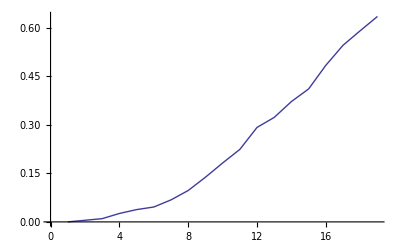

```mathematica
ListLinePlot[%]
```

```mathematica
single = RandomChoice[Range[100], 20]
```

{87,34,3,32,33,27,41,8,62,18,25,56,1,94,68,4,24,64,25,20}

```mathematica
t = Gather[single, Abs[#1 - #2] < 2 &]
```

{{87},{34,33},{3,4},{32},{27},{41},{8},{62},{18},{25,24,25},{56},{1},{94},{68},{64},{20}}

```mathematica
birthdayModelFast[single, 1, 2]
```

0.

```mathematica
t = gatherIntoGroups[single, 0]
```

{{87},{34},{3},{32},{33},{27},{41},{8},{62},{18},{25,25},{56},{1},{94},{68},{4},{24},{64},{20}}

```mathematica
Length[single]
```

20

```mathematica
probSharing[t, 2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Blog calculation - Simple *)
```

```mathematica
noSharing[d_,n_]:= N[d!/((d-n)! * d^n)];
```

```mathematica
noSharing[365,23]
```

0.492703

```mathematica
exactly2Sharing[d_, n_]:= 1 - noSharing[d,n];
```

```mathematica
exactly2Sharing[365,22]
```

0.475695

```mathematica
d = exactly2Sharing[365,#] & /@ Range[55]
```

{0.,0.00273973,0.00820417,0.0163559,0.0271356,0.0404625,0.0562357,0.0743353,0.0946238,0.116948,0.141141,0.167025,0.19441,0.223103,0.252901,0.283604,0.315008,0.346911,0.379119,0.411438,0.443688,0.475695,0.507297,0.538344,0.5687,0.598241,0.626859,0.654461,0.680969,0.706316,0.730455,0.753348,0.774972,0.795317,0.814383,0.832182,0.848734,0.864068,0.87822,0.891232,0.903152,0.91403,0.923923,0.932885,0.940976,0.948253,0.954774,0.960598,0.96578,0.970374,0.974432,0.978005,0.981138,0.983877,0.986262}

```mathematica
g1 = ListLinePlot[d]
```